## Attenuators in both the arms of Mach-Zehnder

## Setup

#### Beam splitter transformation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}};
```

```mathematica
(* Creation operators are representated by c *)
```

#### First beam splitter

```mathematica
{ca0,cb0}=B[1/(√2),1/(√2)].{ca1,cb1};
```

#### Phase shift in lower path

```mathematica
cb1=ⅇ^(-ⅈ ϕ)cb2;
```

#### Second and ‘Fourth’ beam splitters

```mathematica
{ca1,cc1}=B[𝓇,𝓉].{ca2,cc2};
{cb2,cd1}=B[𝓇,𝓉].{cb3,cd2};
```

#### Third beam splitter

```mathematica
{cc2,cd2}=B[1/(√2),1/(√2)].{cc3,cd3};
```

## 1. Single-Mode Squeezed Vacuum

### SMSV in mode a

```mathematica
ClearAll[S,out]
S[ξ_,n_]=1/(√Cosh[ξ])∑_(k=0)^n √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!)); (* Source: Wikipedia*)
(* S[ξ,n] approximates single mode squeezed vacuum up to photon number = 2n *)
out[ca2_,cb3_,n_]=S[ξ,n];
Prob[n_,ξ_]=Sech[ξ]∑_(k=0)^n Binomial[2k,k](Tanh[ξ]/2)^(2k);
```

### Result (BS1,3 are 50-50 beam splitters and we post select on modes a and b having vacuum)

```mathematica
cof=CoefficientList[Expand[out[ca2,cb3,2]],{ca2,cb3}];
cof2=CoefficientList[Collect[Simplify[cof[[1,1]]],{cc3,cd3}],{cc3,cd3}];
Simplify[cof2[[1,1]]]
{Simplify[cof2[[2,1]]],Simplify[cof2[[1,2]]]}
Simplify[cof2[[2,2]]]
{Simplify[cof2[[3,1]]],Simplify[cof2[[1,3]]]}
Simplify[cof2[[3,3]]]
```

1/(√Cosh[ξ])

{0,0}

(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2))

{-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)),-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2))}

(3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2))

So the output state is

1/(√Cosh[ξ])0,0
+ ((ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ)) 𝓇^2 Sinh[ξ])/(4 Cosh[ξ]^(3/2)))1,1
+ √2(-(ⅇ^(-2 ⅈ ϕ) (-1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))2,0
+√2(-(ⅇ^(-2 ⅈ ϕ) (1+ⅇ^(ⅈ ϕ))^2 𝓇^2 Sinh[ξ])/(8 Cosh[ξ]^(3/2)))0,2
+2((3 ⅇ^(-4 ⅈ ϕ) (-1+ⅇ^(2 ⅈ ϕ))^2 𝓇^4 Sinh[ξ]^2)/(64 Cosh[ξ]^(5/2)))2,2
+ …

### Observing interference with and without postselection on modes a and b

#### c=1,d=1

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=5;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

```mathematica
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
```

{0.0729491,{𝓇→0.609028,ξ→7.23793}}

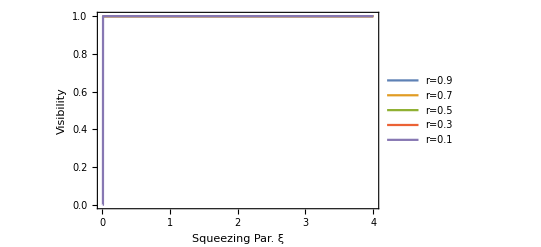

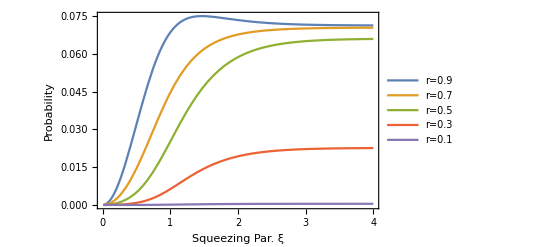

```mathematica
ClearAll[𝓇,ξ]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

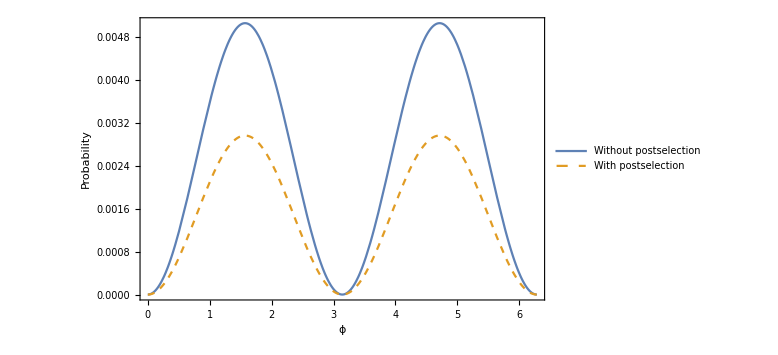

```mathematica
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

#### c=2,d=2

```mathematica
ClearAll[n,a,b,c,d,wopostselect,wpostselect]
n=10;  (* Squeezed states approximated with 2n terms *)
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=2; (* amplitude for mode c chosen to observe the interference  *)
d=2;(* amplitude for mode d chosen to observe the interference  *)
wopostselect[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[Total[coefftable]]/Prob[n,ξ]
];
wpostselect[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out[ca,cb,n],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
Vwo[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wopostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=FindMaximum[wpostselect[x,𝓇,ξ],{x,3 π/4}][[1]];
Imin = FindMinimum[wpostselect [x,𝓇,ξ],{x,3 π/4}][[1]];
N[(Imax-Imin)/(Imax+ Imin)]
];
(*Manipulate[Plot[{wopostselect [ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},PlotLabel-> "Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>")",AxesLabel-> {ϕ,P},PlotLegends->{"Without postselection","With postselection"},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},PlotStyle-> {Solid,Dashed},PlotRange->Full,ImageSize->Medium],{ξ,5,10,Appearance-> "Open"},{𝓇,0.1,1,Appearance-> "Open"}]*)
```

{0.0419302,{𝓇→1.,ξ→1.61082}}

FindMaximum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a maximum; it may be a minimum or a saddle point.

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

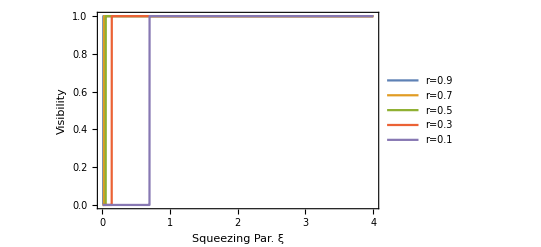

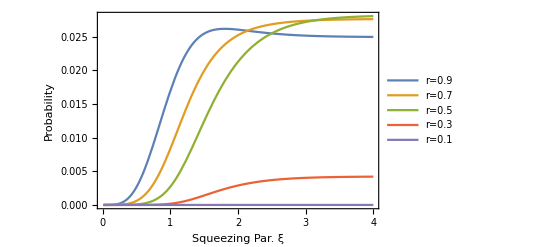

```mathematica
ClearAll[𝓇,ξ]
FindMaximum[{wopostselect[π/2,𝓇,ξ],0≤𝓇≤1&&0<ξ},{𝓇,0.5},{ξ,1}]
Plot[{Vwo[0.9,ξ],Vwo[0.7,ξ],Vwo[0.5,ξ],Vwo[0.3,ξ],Vwo[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect[π/2,0.9,ξ],wopostselect[π/2,0.7,ξ],wopostselect[π/2,0.5,ξ],wopostselect[π/2,0.3,ξ],wopostselect[π/2,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.30]]
ClearAll[𝓇,ξ]
```

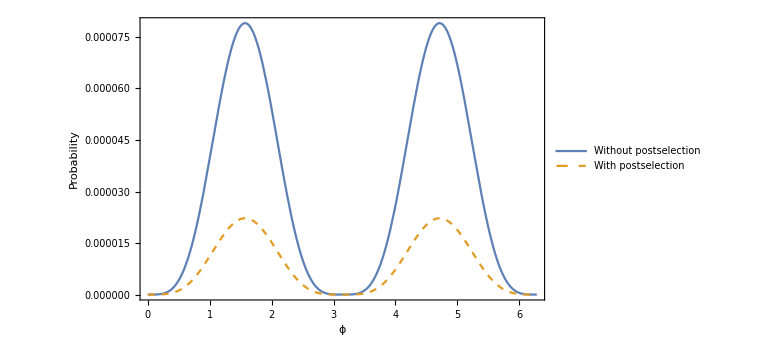

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=0.5;
Plot[{wopostselect[ϕ,𝓇,ξ],wpostselect[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo[𝓇,ξ]]<>" , "<>ToString[Vw[𝓇,ξ]]<>") for 𝓇=0.5, ξ=1.462"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## 2. Two-Mode Squeezed Vacuum Input and observing interference for P(1,1)

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k(ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
ClearAll[out2,n]
n=5;
out2[ca2_,cb3_]=1/Cosh[ξ] Sum[(-ⅈ Tanh[ξ]/1 ca0 cb0)^k/k!,{k,0,n}];
Prob[n_,ξ_]=Sech[ξ]^2(1-Tanh[ξ]^(2(n+1)))/(1-Tanh[ξ]^2);
```

```mathematica
(* Approximation of taking only a few terms *)
```

```mathematica
ClearAll[a,b,c,d,wopostselect2,wpostselect2]
a=0;  (* postselection on mode a *)
b=0;  (* postselection on mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
wopostselect2[ϕ_,𝓇_,ξ_] = Module[{coeffψ,coefftable},
𝓉=√(1-𝓇^2);
coeffψ =√(c!d!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}];
coefftable=Table[Abs[√((i-1)!   (j-1)!)coeffψ[[i,j]]]^2,{i,1,Dimensions[coeffψ][[1]]},{j,1,Dimensions[coeffψ][[2]]}];
Total[coefftable,2]/Prob[n,ξ]
];
wpostselect2[ϕ_,𝓇_,ξ_]=Module[{},
𝓉=√(1-𝓇^2);
Abs[√(c!d! a!b!)CoefficientList[CoefficientList[out2[ca,cb],{cc3,cd3}][[c+1,d+1]],{ca,cb}][[a+1,b+1]]]^2/Prob[n,ξ]
];
(* Visibility *)
Vwo2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wopostselect2 [0,𝓇,ξ];
Imin =wopostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
Vw2[𝓇_,ξ_]:=Module[{Imax,Imin},
Imax=wpostselect2 [0,𝓇,ξ];
Imin =wpostselect2 [Pi/2,𝓇,ξ];
N[(Imax-Imin)/(Imax+ Imin)]
];
```

ϕ=π/2

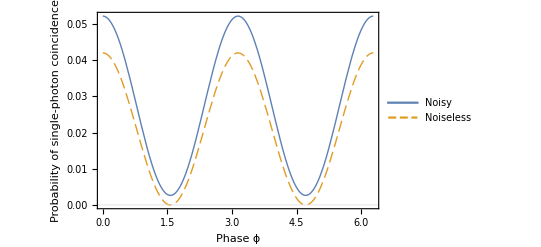

```mathematica
Plot[{wopostselect2[ϕ,√0.5,0.5],wpostselect2[ϕ,√0.5,0.5]},{ϕ,0,2π},PlotRange->{0,Full},Frame->True,GridLines->{None,{0}},FrameLabel->{"Phase ϕ","Probability of single-photon coincidence","Interference "},LabelStyle-> {Black,Large},PlotLegends->Placed[{"Noisy","Noiseless"},{0.75,0.8}],LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.65],PlotStyle->{Thick,{Thick,Dashing[{0.02,0.009}]}},GridLinesStyle->{Thick,Black},FrameStyle->Thick]
```

ϕ=π

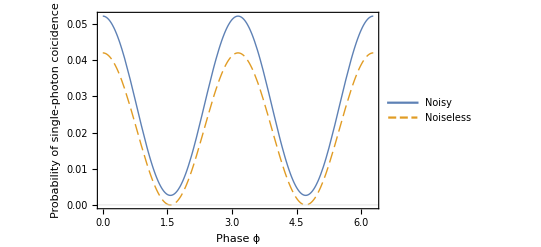

```mathematica
Plot[{wopostselect2[ϕ,√0.5,0.5],wpostselect2[ϕ,√0.5,0.5]},{ϕ,0,2π},PlotRange->{0,Full},Frame->True,GridLines->{None,{0}},FrameLabel->{"Phase ϕ","Probability of single-photon coicidence","Interference "},LabelStyle-> {Black,Large},PlotLegends->Placed[{"Noisy","Noiseless"},{0.75,0.8}],LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.65],PlotStyle->{Thick,{Thick,Dashing[{0.02,0.009}]}},GridLinesStyle->{Thick,Black},FrameStyle->Thick]
```

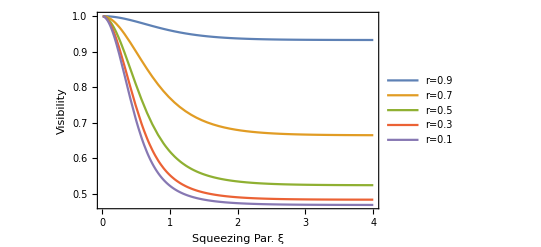

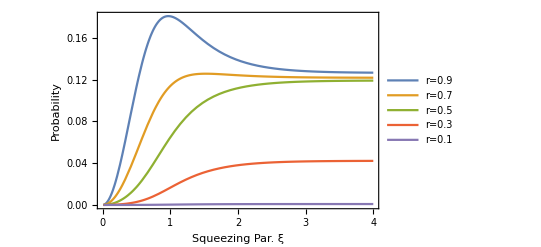

```mathematica
Plot[{Vwo2[0.9,ξ],Vwo2[0.7,ξ],Vwo2[0.5,ξ],Vwo2[0.32,ξ],Vwo2[0.1,ξ]},{ξ,0.01,4},PlotRange->Full,Frame->True,GridLines->{ {},{}},FrameLabel->{"Squeezing Par. ξ","Visibility","Vis. w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,ImageSize->Scaled[0.25]]
Plot[{wopostselect2[0,0.9,ξ],wopostselect2 [0,0.7,ξ],wopostselect2[0,0.5,ξ],wopostselect2[0,0.3,ξ],wopostselect2[0,0.1,ξ]},{ξ,0.01,4},PlotRange->{0,Full},Frame->True,FrameLabel->{"Squeezing Par. ξ","Probability","Max Prob. of Success w/o Post-selection"},PlotLegends->{"r=0.9","r=0.7","r=0.5","r=0.3","r=0.1"},LabelStyle->Large,GridLines-> {{},{}},ImageSize->Scaled[0.30]]
```

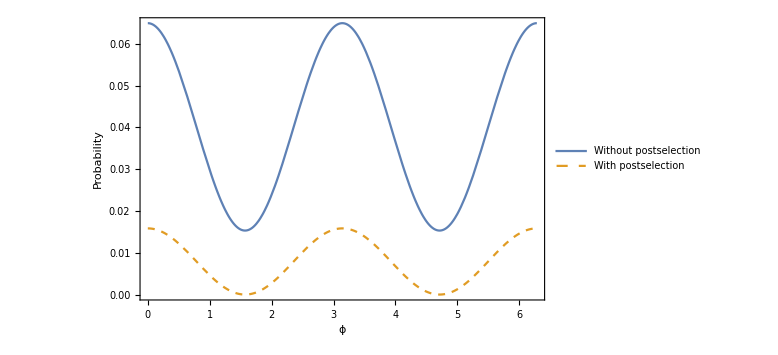

```mathematica
ClearAll[𝓇,ξ]
𝓇=0.5;
ξ=1;
Plot[{wopostselect2[ϕ,𝓇,ξ],wpostselect2[ϕ,𝓇,ξ]},{ϕ,0,2π},FrameLabel-> {"ϕ","Probability","Visibility (w/o , w ) postselection = ("<>ToString[Vwo2[𝓇,ξ]]<>" , "<>ToString[Vw2[𝓇,ξ]]<>")"},Frame-> True,PlotLegends->{"Without postselection","With postselection"},PlotStyle-> {Solid,Dashed},PlotRange->{0,Automatic},Ticks->{{0,π/2,π,(3π)/2,2π},Automatic},ImageSize->Large,LabelStyle->Large]
ClearAll[𝓇,ξ]
```

## Squeezed states through Noiseless Attenuation

## Original

```mathematica
ClearAll[matsq,ξ,k,x]
ψsq[ξ_,nlim_,x_]=1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k(ⅇ^(-x^2/2)/(π^(1/4)√((2k)!2^(2k))))HermiteH[2k,x];(*ca0^(2k)/(√((2k)!));*)
nlim=10;
Wsq[ξ_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψsq[ξ,nlim,x-y/2])] ψsq[ξ,nlim,x+y/2],{y,-10,10}];
limits=3;
range=10;
s=3;
ξ=1/2 Log[s];
Monitor[
matsq=Table[Re[Chop[Wsq[ξ,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

```mathematica
Dimensions[matsq]
```

{21,21}

#### s = 3

```mathematica
ListPlot3D[matsq,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

Model Fitting

```mathematica
ClearAll[a,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[matsq][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matsq[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→3.}

## After beam splitter

```mathematica
ClearAll[s,ξ,r,t,ca,cb,nlim]
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[ξ_,nlim_]=Expand[1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!))];
b=0;(* Post selection *)
s=3;
ξ=1/2 Log[s];
nlim=10;
coefftable=CoefficientList[ψin[ξ,nlim],{cb,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];
Dimensions[coefftable]
```

{21,21}

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=3;
range=10;
Monitor[
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wpsmat,2](limits/range)^2
```

0.999472

𝓇=√0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→1.66667}

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];

𝓇=√0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
limits=3;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wopsmat,2](limits/range)^2
```

0.998432

𝓇=√0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wopsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wopsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.275664,σ→0.759836,s→1.73205}

```mathematica
{√(1/(π a/.fit)),(√2 σ/.fit)^1}
```

{1.07457,1.07457}

## Cat States through noiseless attenuation

### Calculation of the Wigner function using number states (and approx. by taking few terms) before Noiseless Attenuation

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n (ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x] )/(√n!);
ψcExact[α_,nlim_,x_]=(1/π^(1/4))ⅇ^((-(x-√2 α)^2)/2);(*checked*)
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√(2(1+ⅇ^(-2 Abs[α]^2))));

nlim=20;
WCat[α_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψCat[α,nlim,x-y/2])] ψCat[α,nlim,x+y/2],{y,-10,10}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
```

```mathematica
limits=5;
range=10;
α=2;
matCatExact2=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

```mathematica
Monitor[
matCat=Table[Re[Chop[WCat[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}]
```

$Aborted

```mathematica
NIntegrate[WCat[2,0,x,p],{x,-5,5},{p,-5,5}]
```

0.998934

```mathematica
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

```mathematica
N[Total[Total[matCatExact2]]](limits/range)^2
```

0.99977

### Calculation of the Wigner function using number states (and approx. by taking few terms) after Noiseless Attenuation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,nlim_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];
OptoN = Table[√((i-1)!(j-1)!),{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}];
Pr=Chop[(OptoN coefftable)*  (OptoN coefftable)];
(*Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];*)
Dimensions[coefftable]
NumberStates[x_]=Table[ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}];
```

{21,21}

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[OptoN[[b+1,All]] coefftable[[b+1,All]] NumberStates[x]]];
```

```mathematica
(*ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];*)
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=5;
range=10;
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
Total[wpsmat,2](limits/range)^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.000155416}. NIntegrate obtained 7.058×10^-16-2.38228×10^-22 ⅈ and 2.99291×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained -1.19405×10^-15+6.56451×10^-21 ⅈ and 6.13448×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {-0.0587492}. NIntegrate obtained -1.6465×10^-13-1.69407×10^-20 ⅈ and 4.78921×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.999999

r = √0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[(coefftable OptoN)[[i,j]] NumberStates[x][[j]],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}] ,{2}];
(*Total[ coefftable OptoN  ConstantArray[NumberStates[x],Dimensions[coefftable][[1]]],{2}];*)
(*ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];*)
Dimensions[ψoutwops[x]]
```

{21}

#### results

```mathematica
𝓇=0;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
```

```mathematica
limits=5;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}],
{p,x}];
Total[wopsmat,2](limits/range)^2
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

0.999831

r = √0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

## Model fitting

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### Before

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[matCatExact2][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matCatExact2[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{A→1.,α→2.}

```mathematica
limits=5;
range=10;
α=α/.fit;
matCatExact=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### After (w/ post selection)

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
limits=5;
range=10;
matCatExact2=Table[Re[Chop[WCatExact[α/.fit,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

{A→1.,α→1.41422}

-Graphics3D-

This tells the cat state is noiseless after post selection

## Effect of inefficient detector in noiseless attenuation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb1};
{cb1,cdump0}=B[𝓇loss,𝓉loss].{cb,cdump};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,n_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)Simplify[ca0^n] )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,cdump,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!(k-1)!)coefftable[[i,j,k]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]},{k,1,Dimensions[coefftable][[3]]}]];
Dimensions[coefftable]
```

{21,21,21}

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!(j-1)!)coefftable[[b+1,i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]];
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
𝓇loss=√(2/3);
𝓉loss=√(1-𝓇loss^2);
Wwpsp[x_,p_]:=(1/(Total[Pr,{2,3}][[b+1]]))(1/(2π))Total[Table[NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y][[i]])] ψoutwps[x+(1/2)y][[i]],{y,-10,10}],{i,1,Dimensions[coefftable][[2]]}]];
(*Wwpsp[x_,p_]:=∑_(i=1)^(Dimensions[coefftable][[2]]) (1/(Total[Pr,{3}][[b+1,i]]))(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwps[x-(1/2)y][[i]])^*ψoutwps[x+(1/2)y][[i]],{y,-10,10}];*)

limits=5;
range=10;
Monitor[
wpsmatineff=Table[Re[Chop[Wwpsp[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 7.05801×10^-16-6.94832×10^-23 ⅈ and 3.7425×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 1.60994×10^-15-2.87859×10^-22 ⅈ and 5.5369×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 8.49223×10^-16+5.82335×10^-22 ⅈ and 2.27481×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Total[wpsmatineff,2](limits/range)^2
```

0.999999

r = √0.5, loss = 100%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 75%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss =66.67%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 50%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss =33.33%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

r = √0.5, loss = 25%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 0%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-